# Homework 1

Name:

ID:

## Problem 1

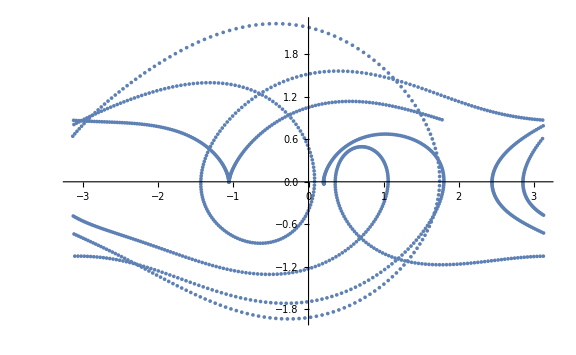

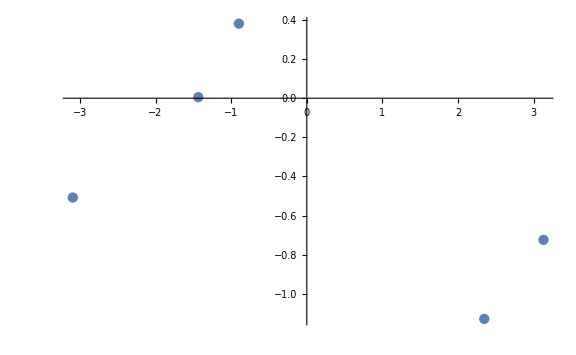

{0,237,472,708,943,1179}

5

```mathematica
ClearAll["Global`*"];
tstart=0; tend=50.; dt=.04; g=9.81; l=9.8; Ω=Sqrt[g/l];mass=0.5; Subscript[F, D]=1.2;
q={0.5,Ω/2,Ω,2 Ω}; lq=Length[q];

Subscript[Ω, D]={2/3,Sqrt[Ω^2- 2 q[[1]]^2],2.5,3};

color={Red,Green,Purple,Orange,Blue};

tlist=Range[tstart,tend,dt];

thetalist=0 tlist;omegalist=0 tlist; lt=Length[tlist];

thetalist1=0 tlist;omegalist1=0 tlist;

thetalist[[1]]=0.21; omegalist[[1]]=0;

thetalist1[[1]]=0.2101; omegalist1[[1]]=0;

Do[omegalist[[i]]=omegalist[[i-1]]-(Ω^2 Sin[thetalist[[i-1]]] -Subscript[F, D] Sin[Subscript[Ω, D][[1]] tlist[[i-1]]]+ q[[1]] omegalist[[i-1]])dt;thetalist[[i]]=thetalist[[i-1]]+omegalist[[i]] dt;

omegalist1[[i]]=omegalist1[[i-1]]-(Ω^2 Sin[thetalist1[[i-1]]] -Subscript[F, D] Sin[Subscript[Ω, D][[1]] tlist[[i-1]]]+ q[[1]] omegalist1[[i-1]])dt;
thetalist1[[i]]=thetalist1[[i-1]]+omegalist1[[i]] dt;

If[thetalist[[i]]>π,thetalist[[i]]=thetalist[[i]]-2 π,If[thetalist[[i]]<-π,thetalist[[i]]=thetalist[[i]]+2 π]];

If[thetalist1[[i]]>π,thetalist1[[i]]=thetalist1[[i]]-2 π,If[thetalist1[[i]]<-π,thetalist1[[i]]=thetalist1[[i]]+2 π]],{i,2,lt}];

Δθ=0 tlist;

Do[Δθ[[i]]=Norm[thetalist[[i]]-thetalist1[[i]]],{i,lt}];

phaselist={0};
(*Do[n=1;Do[If[Norm[tlist[[i]]-(2 n π)/Subscript[Ω, D]]<dt/2,AppendTo[phaselist,i]],{n,1,Floor[(tend Subscript[Ω, D][[1]])/(2 π)]}],{i,lt}]; *)

Do[Do[If[Norm[tlist[[i]]-(2 π n)/(Subscript[Ω, D][[1]])]<dt/2,AppendTo[phaselist,i]],{n,5}],{i,lt}]
newphaselist=Take[phaselist,{2,Length[phaselist]}];
lphaselist=Length[newphaselist];
ωθphaselist=Table[{thetalist[[newphaselist[[i]]]],omegalist[[newphaselist[[i]]]]},{i,lphaselist}];

θtlist=Table[{tlist[[i]],thetalist[[i]]},{i,lt}];
ωtlist=Table[{tlist[[i]],omegalist[[i]]},{i,lt}];

θtlist1=Table[{tlist[[i]],thetalist1[[i]]},{i,lt}];
ωtlist1=Table[{tlist[[i]],omegalist1[[i]]},{i,lt}];

Δθtlist=Table[{tlist[[i]],Δθ[[i]]},{i,lt}];

ωθlist=Table[{thetalist[[i]],omegalist[[i]]},{i,lt}];

(*ListPlot[θtlist]
ListPlot[ωtlist]
ListPlot[θtlist1]
ListPlot[ωtlist1]
ListPlot[Δθtlist,ScalingFunctions->"Log10",ImageSize->Large]*)

ListPlot[ωθlist]

ListPlot[ωθphaselist]

phaselist

Floor[(tend Subscript[Ω, D][[1]])/(2 π)]
```

## Problem 2

## Problem 3

## Problem 4

## Problem 5

## Problem 6

## Problem 7

## Problem 8

## Problem 9

## Problem 10